Experiments performed by Manish J. Thapa under supervision of Dr. Johannes Heinsoo @Quantum Device Lab, ETH Zurich, April 2016

```mathematica
LabelStyle
```

```mathematica
ReadList["1163_chevronLog.dat"];

runNumber=Length[dataTable[[All,1,1,1]]];

states={"ee","gg","ge","eg","fe","ff","ef","gf","fg"};
```

```mathematica
colorschememan=Table[Blend[{ColorData[104,"ColorList"][[5]],ColorData[13,"ColorList"][[2]]},i^2],{i,0,1,0.1}];
```

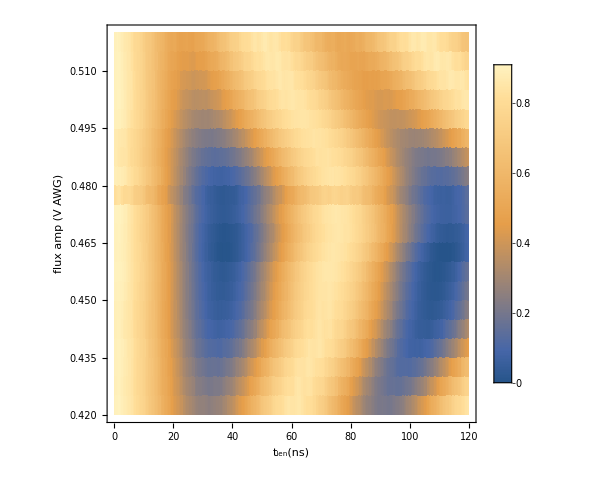

```mathematica
k1=Table[If[runNumber>1,ListDensityPlot[dataTable[[All,i,All,1]],Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->357,LegendMargins->{{0,0},{10,8}},LabelStyle->Directive[Black,24]],Right],PlotRange->{All,All,All},DataRange->{{0,120},{0.42,0.52}},PerformanceGoal->"Quality",FrameLabel->{"t_len(ns)","flux amp (V AWG)"},LabelStyle->Directive[Black,24],TicksStyle->Directive[Orange,15],ImageSize->500,InterpolationOrder->0,GridLinesStyle->Dashed,Method->{"GridLinesInFront"->True}],""],{i,{1}}]//Row
```

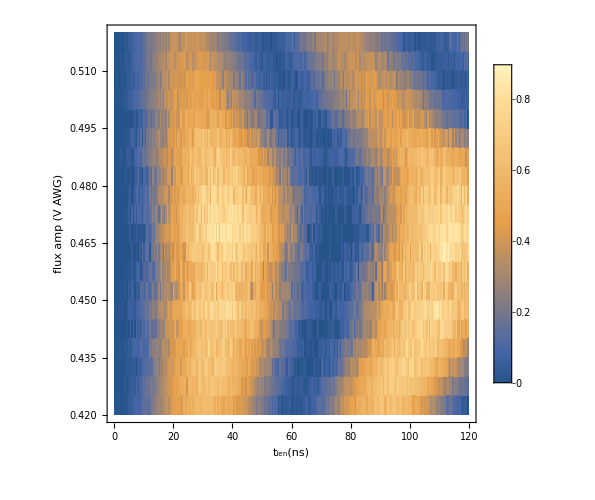

```mathematica
k2=Table[If[runNumber>1,ListDensityPlot[dataTable[[All,i,All,1]],Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->357,LegendMargins->{{0,0},{10,8}},LabelStyle->Directive[Black,24]],Right],PlotRange->{All,All,All},DataRange->{{0,120},{0.42,0.52}},PerformanceGoal->"Quality",FrameLabel->{"t_len(ns)","flux amp (V AWG)"},LabelStyle->Directive[Black,24],TicksStyle->Directive[Orange,10],ImageSize->500,InterpolationOrder->0,GridLinesStyle->Dashed,Method->{"GridLinesInFront"->True}],""],{i,{8}}]//Row
```

```mathematica
Export["newexperiment110.png",k1]
```

newexperiment110.png

```mathematica
Export["newexperiment200.png",k2]
```

newexperiment200.png

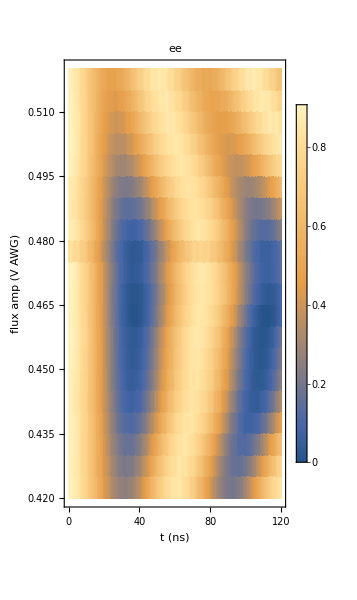
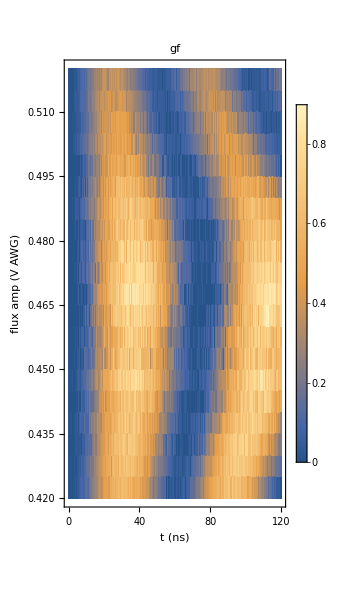

```mathematica
Table[If[runNumber>1,ListDensityPlot[dataTable[[All,i,All,1]],DataRange->{{0,120},{0.42,0.52}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->250],InterpolationOrder->0,PlotRange->Full,ImageSize->300,AspectRatio->2/1,FrameTicks->{{Automatic,freqTicks},{Automatic,Automatic}},PlotLabel->""~~ToString[states[[i]]],FrameLabel->{{"flux amp (V AWG)"},{"t (ns)",""}}],""],{i,{1,8}}]//Row
```